Functional form of the Chabrier IMF:

```mathematica
Mmin=0.08; (* Minimum mass in units of Msun *)
Mmax=120; (* Maximum mass in units of Msun *)
Mbreak=1; (* Break mass in units of Msun *)
Mpeak = 0.2;  (* Peak mass in units of Msun *)
σlog10M = 0.55;  (* Dispersion in Subscript[log, 10] M *)
Γ=-2.35; (* High-mass slope *)
dNdlog10MNonNorm[M_]:=Piecewise[{
{Exp[-(Log10[M]-Log10[Mpeak])^2/(2 σlog10M^2)],Mmin<=M && M<Mbreak},
{Exp[-(Log10[Mbreak]-Log10[Mpeak])^2/(2 σlog10M^2)] (M/Mbreak)^(Γ+1),Mbreak<=M && M<Mmax}},
0
]; (* Chabrier IMF -- note that this is NOT properly normalized *)
```

Now compute the normalization. To understand this step, recall that ∫_M0^M1 dN/(dlog(M))ⅆM is the mass in stars from M0 to M1, not the number of stars, since dN/dlog(M) ∝ M dN/dM. Thus if we normalize such that ∫_0^∞ dN/(dlog(M))ⅆM = 1, we can interpret ∫_M0^M1 dN/(dlog(M))ⅆM as the fraction of the stellar mass that lies in some mass interval (M0,M1).

```mathematica
norm=1/Integrate[dNdlog10MNonNorm[M],{M,Mmin,Mmax}]; (* Normalization *)
dNdlog10M[M_]=norm dNdlog10MNonNorm[M]; (* Properly normalized Chabrier IMF *)
```

Plot of the Chabrier IMF:

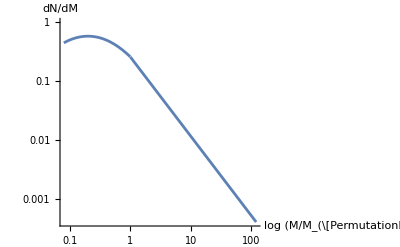

```mathematica
LogLogPlot[dNdlog10M[M],{M,Mmin,Mmax},AxesLabel->{"log (M/M_(\[PermutationProduct]))","dN/dM"}]
```

Calculate fraction of mass in stars more massive than 9 M_(\[PermutationProduct]):

```mathematica
Mhigh=9; (* "High" mass value in Msun -- stars above this mass can have SNe *)
fhigh=Integrate[dNdlog10M[M],{M,Mhigh,Mmax}]
```

0.205495

Now calculate the mean mass of star more massive than 9 M_(\[PermutationProduct]). To do this calculation, recall that ∫_M0^M1 dN/(dlog(M))ⅆlogM∝∫_M0^M1 1/M dN/(dlog(M))ⅆM is the number of stars from M0 to M1. Thus the quantity we want is

```mathematica
MstarHighMean=fhigh/Integrate[dNdlog10M[M]/M,{M,Mhigh,Mmax}]
```

21.3397